```mathematica
Needs["xAct`xPert`"];

BlackHole="EMsolution";

pathNotebooks=NotebookDirectory[];
```

## AdS_4 Logs

This is the main file where the Seeley-DeWitt coefficients are computed. The functions needed for the computation are in Functions.nb. The background-specific rules are in EMsolution.nb.

## Initialization

### xAct

```mathematica
DefManifold[M4,4,IndexRange[a,h]];
DefVBundle[Spinor,M4,4,{α,β,γ,δ,λ,ρ,σ,σ1,σ2,σ3,σ4,σ5,σ6,σ7,σ8,σ9}]
AddIndices[TangentM4,{h1,h2,h3,h4,h5,h6,w1,w2,w3,w4,w5,w6,w7,w8,w9,y1,y2,y3,y4,y5,y6,y7,y8,y9}];
DefMetric[1,gmn[-a,-b],CD,PrintAs->"g"];
DefTensor[gamma[a,-α,β],{M4},PrintAs->"γ"];
DefTensor[gamma5[-α,β],{M4},PrintAs->"γ^5"];
DefTensor[ksdummy[],{M4}]
DefTensor[kmndummy[],{M4}]
DefTensorPerturbation[ks[LI["order"]],ksdummy[],{M4},PrintAs->"k"];
DefTensorPerturbation[kmn[LI["order"],-a,-b],kmndummy[-a,-b],{M4},PrintAs->"k"];
DefMetricPerturbation[gmn,hmn,PrintAs->"h"];

DefConstantSymbol[Lambda,PrintAs->"Λ"];
DefConstantSymbol[lAdS];
DefConstantSymbol[Δ];
DefConstantSymbol[m]
DefConstantSymbol[m2];

DefConstantSymbol[swickGravity,PrintAs->"sG"];
AutomaticRules[swickGravity,Table[swickGravity^(2i)->1,{i,5}]];
DefConstantSymbol[swick,PrintAs->"s"];
AutomaticRules[swick,Table[swick^(2i)->1,{i,5}]];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefVBundle: Defining vbundle Spinor.

** DefTensor: Defining symmetric metric tensor gmn[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilongmn[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmn[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetragmn†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detgmn[]. Determinant.

** DefTensor: Defining tensor gamma[a,-α,β].

** DefTensor: Defining tensor gamma5[-α,β].

** DefTensor: Defining tensor ksdummy[].

** DefTensor: Defining tensor kmndummy[].

** DefTensor: Defining tensor ks[LI[order]].

** DefTensor: Defining tensor kmn[LI[order],-a,-b].

** DefParameter: Defining parameter PerturbationParametergmn.

** DefTensor: Defining tensor hmn[LI[order],-a,-b].

** DefConstantSymbol: Defining constant symbol Lambda.

** DefConstantSymbol: Defining constant symbol lAdS.

** DefConstantSymbol: Defining constant symbol Δ.

** DefConstantSymbol: Defining constant symbol m.

** DefConstantSymbol: Defining constant symbol m2.

** DefConstantSymbol: Defining constant symbol swickGravity.

Rules {1,1,2,1,3,1,4,1,5,1} have been declared as UpValues for sG.

** DefConstantSymbol: Defining constant symbol swick.

Rules {1,1,2,1,3,1,4,1,5,1} have been declared as UpValues for s.

### Fields

#### Gauge field

```mathematica
DefTensor[Fc[-a,-b],{M4},Antisymmetric[{1,2}],PrintAs->"F"];
DefTensor[Ftc[-a,-b],{M4},Antisymmetric[{1,2}],PrintAs->"F̃"];
DefTensor[Ac[-a],{M4},PrintAs->"A"];

DefTensor[F1[-a,-b],{M4},Antisymmetric[{1,2}],PrintAs->"F_1"];
DefTensor[Ft1[-a,-b],{M4},Antisymmetric[{1,2}],PrintAs->"OverTilde[F_1]"];
DefTensor[A1[-a],{M4},PrintAs->"A_1"];
DefTensorPerturbation[f1[LI["order"],-a,-b],F1[-a,-b],{M4},PrintAs->"f_1"];
DefTensorPerturbation[ft1[LI["order"],-a,-b],Ft1[-a,-b],{M4},PrintAs->"(f̃)_1"];
DefTensorPerturbation[a1[LI["order"],-a],A1[-a],{M4},PrintAs->"a_1"];
```

** DefTensor: Defining tensor Fc[-a,-b].

** DefTensor: Defining tensor Ftc[-a,-b].

** DefTensor: Defining tensor Ac[-a].

** DefTensor: Defining tensor F1[-a,-b].

** DefTensor: Defining tensor Ft1[-a,-b].

** DefTensor: Defining tensor A1[-a].

** DefTensor: Defining tensor f1[LI[order],-a,-b].

** DefTensor: Defining tensor ft1[LI[order],-a,-b].

** DefTensor: Defining tensor a1[LI[order],-a].

#### Ghosts

```mathematica
DefTensor[cvec[LI[1],a],{M4},PrintAs->"c"];
DefTensor[bvec[LI[1],a],{M4},PrintAs->"b"];
DefTensor[csca0[LI[1]],{M4},PrintAs->"c_0"];
DefTensor[bsca0[LI[1]],{M4},PrintAs->"b_0"];
```

** DefTensor: Defining tensor cvec[LI[1],a].

** DefTensor: Defining tensor bvec[LI[1],a].

** DefTensor: Defining tensor csca0[LI[1]].

** DefTensor: Defining tensor bsca0[LI[1]].

### Rules and definitions

```mathematica
DualRules=Join[MakeRule[{Ftc[-a,-b],1/2 epsilongmn[-a,-b,-c,-d] Fc[c,d]}]];
```

```mathematica
HermitianRules=Join[
MakeRule[{swickGravity,-swickGravity}],
MakeRule[{Ftc[-a,-b],-Ftc[-a,-b]}],
MakeRule[{gamma[LI[5],-α,β],gamma[LI[5],-α,β]}],
MakeRule[{gamma5[-α,β],gamma5[-α,β]}],
MakeRule[{epsilongmn[a,b,c,d],epsilongmn[a,b,c,d]}]];
LorentzHermitianRules=Join[
MakeRule[{Ftc[-a,-b],-Ftc[-a,-b]}]];
```

```mathematica
gammaU=gamma[a,-α,β];
gammaUU=1/2(gamma[a,-α,λ]gamma[b,-λ,β]-gamma[b,-α,λ]gamma[a,-λ,β]);
gammaUUUU=Antisymmetrize[gamma[a,-α,λ]gamma[b,-λ,ρ]gamma[c,-ρ,σ]gamma[d,-σ,β],{a,b,c,d}];
GUUUU=1/2(gmn[-a,c]gmn[-b,d]+gmn[-a,d]gmn[-b,c]-1/2 gmn[-a,-b]gmn[c,d]);
Rs=RicciScalarCD[];
RicRic=RicciCD[a,b]RicciCD[-a,-b];
RR=RiemannCD[a,b,c,d]RiemannCD[-a,-b,-c,-d];

ProjL=1/2(gamma[LI[6],-α,β]+gamma[LI[5],-α,β]);
ProjR=1/2(gamma[LI[6],-α,β]-gamma[LI[5],-α,β]);
Pgrav=gmn[a,b]gamma[LI[6],-α,β]-1/4 gamma[a,-α,γ]gamma[b,-γ,β];
```

### Dependencies

```mathematica
NotebookEvaluate[pathNotebooks<>"Functions.nb"];
NotebookEvaluate[pathNotebooks<>BlackHole<>".nb"];
```

## Minimally coupled fields

### Free scalar

```mathematica
{nG,nS}={0,1};
Bbase={0};

BP={{m2}};
Bom={{0}};

BE=ComputeE[BP,Bbase,Bom]//Simp;
BTrE=TrE[BE,Bbase]//Simp;
BTrEE=TrSq[BE,Bbase]//Simp;

BOm=ComputeOm[Bom,Bbase]//Simp;
BTrOmOm=TrSqO[BOm,Bbase];

BTrOne=4nG+nS;

a0S=BTrOne;
a2Sraw=BTrE+BTrOne/6 Rs;
a4Sraw=1/2 BTrEE+1/6 Rs BTrE+1/12 BTrOmOm+BTrOne/360(5 Rs^2+2RR-2RicRic);
```

```mathematica
a0S
a2S=a2Sraw/.m2->Δ(Δ-3)//TC
a4S=a4Sraw/.m2->Δ(Δ-3)//FC
```

1

1/12 (2+3 Δ-Δ^2) R[▽]

-1/180 R[▽] |   |  
a | b R[▽] | a | b
  |  +1/288 (4+12 Δ+5 Δ^2-6 Δ^3+Δ^4) R[▽]^2+1/180 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4S//FDecompose//FullSimplify
```

Remains: 0

Value: -Euler/360+Weyl^2/120+1/288 (-2-3 Δ+Δ^2)^2 R[▽]^2

{-1/360,1/120,1/288 (-2+(-3+Δ) Δ)^2,0}

### Free fermion

```mathematica
{nGrav,nGaug}={0,1};
Fbase={0};
FL={{m gamma[LI[6],-α,β]}};

FP=fComputeP[FL,Fbase]//gSimp;
Fom=fComputeom[FL,Fbase]//gSimp;

FE=fComputeE[FP,Fbase,Fom]//gSimp//fSimp;
FTrE=fTr[TrE[FE,Fbase]]//gSimp//fSimp;
FTrEE=fTrSq[FE,Fbase]//gSimp//fSimp;

FOm=fComputeOm[Fom,Fbase]//gSimp//fSimp;
FTrOmOm=fTrSqO[FOm,Fbase]//gSimp//fSimp;

FTrOne= 16nGrav +4 nGaug ;

a0FM=(-1/2)FTrOne;
a2FMraw=(-1/2)(FTrE+FTrOne/6 Rs);
a4FMraw=(-1/2)(1/2 FTrEE +1/6 Rs FTrE+1/12 FTrOmOm+FTrOne/360( 5 Rs^2+2RR-2RicRic))//fSimp;
```

```mathematica
a0FD=2a0FM
a2FD=2a2FMraw/.m->Δ-3/2//TC
a4FD=2a4FMraw/.m->Δ-3/2//FC
```

-4

1/12 (-5+12 Δ-4 Δ^2) R[▽]

1/45 R[▽] |   |  
a | b R[▽] | a | b
  |  +((-25+120 Δ-184 Δ^2+96 Δ^3-16 Δ^4) R[▽]^2)/1152+7/360 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4FD//FDecompose
```

Remains: 0

Value: -(11 Euler)/360+Weyl^2/20-((3-2 Δ)^2 (1-12 Δ+4 Δ^2) R[▽]^2)/1152

{-11/360,1/20,-((3-2 Δ)^2 (1-12 Δ+4 Δ^2))/1152,0}

### Free vector

```mathematica
{nG,nS}={1,0};
Bbase={1};

BP={{-RicciCD[-a,-b]}};
Bom={{0}};

BE=ComputeE[BP,Bbase,Bom]//Simp;
BTrE=TrE[BE,Bbase]//Simp;
BTrEE=TrSq[BE,Bbase]//Simp;

BOm=ComputeOm[Bom,Bbase]//Simp;
BTrOmOm=TrSqO[BOm,Bbase];

BTrOne=4nG+nS;

a0Vraw=BTrOne;
a2Vraw=BTrE+BTrOne/6 Rs;
a4Vraw=1/2 BTrEE+1/6 Rs BTrE+1/12 BTrOmOm+BTrOne/360(5 Rs^2+2RR-2RicRic);

a0Vghosts=-2a0S/.m2->0;
a2Vghosts=-2a2Sraw/.m2->0;
a4Vghosts=-2a4Sraw/.m2->0;
```

```mathematica
a0V=a0Vraw+a0Vghosts
a2V=a2Vraw+a2Vghosts//TC
a4V=a4Vraw+a4Vghosts//FC
```

2

-(2 R[▽])/3

22/45 R[▽] |   |  
a | b R[▽] | a | b
  |  -(5 R[▽]^2)/36-13/180 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4V//FDecompose
```

Remains: 0

Value: -(31 Euler)/180+Weyl^2/10

{-31/180,1/10,0,0}

### Free Rarita-Schwinger field

```mathematica
{nGrav,nGaug}={1,0};
Fbase={1};

FL={{gmn[a,b]gamma[LI[6],-α,β]}};

FP=fComputeP[FL,Fbase]//gSimp;
Fom=fComputeom[FL,Fbase]//gSimp;

FE=fComputeE[FP,Fbase,Fom]//gSimp//fSimp;
FTrE=fTr[TrE[FE,Fbase]]//gSimp//fSimp;
FTrEE=fTrSq[FE,Fbase]//gSimp//fSimp;

FOm=fComputeOm[Fom,Fbase];
FTrOmOm=fTrSqO[FOm,Fbase];

FTrOne= 16nGrav +4 nGaug ;

a0RSraw=(-1/2)FTrOne;
a2RSraw=(-1/2)(FTrE+FTrOne/6 Rs);
a4RSraw=(-1/2)(1/2 FTrEE +1/6 Rs FTrE+1/12 FTrOmOm+FTrOne/360( 5 Rs^2+2RR-2RicRic))//fSimp;

a0RSghosts=-3a0FM/.m->0;
a2RSghosts=-3a2FMraw/.m->0;
a4RSghosts=-3a4FMraw/.m->0;
```

```mathematica
a0RS=a0RSraw+a0RSghosts
a2RS=a2RSraw+a2RSghosts//TC
a4RS=a4RSraw+a4RSghosts//FC
```

-2

-R[▽]/2

1/90 R[▽] |   |  
a | b R[▽] | a | b
  |  +R[▽]^2/48-233/720 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4RS//FDecompose
```

Remains: 0

Value: (229 Euler)/720-(77 Weyl^2)/120-R[▽]^2/12

{229/720,-77/120,-1/12,0}

### Summary for massless fields

```mathematica
DefConstantSymbol[NS,PrintAs->"n_S"];
DefConstantSymbol[NF,PrintAs->"n_F"];
DefConstantSymbol[NV,PrintAs->"n_V"];
DefConstantSymbol[NG,PrintAs->"n_(3/2)"];
```

** DefConstantSymbol: Defining constant symbol NS.

** DefConstantSymbol: Defining constant symbol NF.

** DefConstantSymbol: Defining constant symbol NV.

** DefConstantSymbol: Defining constant symbol NG.

```mathematica
a4massless=NS (a4S/.Δ->3)+NF (a4FD/.Δ->3/2)+NV a4V+NG a4RS//FC
```

1/180 (4 n_F+2 n_(3/2)-n_S+88 n_V) R[▽] |   |  
a | b R[▽] | a | b
  |  +1/144 (-2 n_F+3 n_(3/2)+2 n_S-20 n_V) R[▽]^2+1/720 (14 n_F-233 n_(3/2)+4 n_S-52 n_V) R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4massless//FDecompose//FullSimplify
```

Remains: 0

Value: 1/120 Weyl^2 (6 n_F-77 n_(3/2)+n_S+12 n_V)+1/720 Euler (-22 n_F+229 n_(3/2)-2 (n_S+62 n_V))+1/72 (-6 n_(3/2)+n_S) R[▽]^2

{1/720 (-22 n_F+229 n_(3/2)-2 (n_S+62 n_V)),1/120 (6 n_F-77 n_(3/2)+n_S+12 n_V),1/72 (-6 n_(3/2)+n_S),0}

```mathematica
a2massless=NS (a2S/.Δ->3)+NF (a2FD/.Δ->3/2)+NV a2V+NG a2RS//FC
```

1/72 (-2 n_F+3 n_(3/2)-n_S+4 n_V) R[▽]^2

## Einstein-Maxwell theory

### Lagrangian

We give the Lagrangian used by xPert to extract the bosonic fluctuations. The Einstein-Hilbert term is already included (normalized as √g R).

```mathematica
LGR=Sqrt[Detgmn[]](-1/4 F1[-a,-b]F1[a,b]-2Lambda)
```

√(g^OverTilde[~]) (-2 Λ-1/4 F_1 |   |  
a | b F_1 | a | b
  |  )

### Bosons

```mathematica
nG=1;nS=0;

gaugeFields={f1};
tgaugeFields={ft1};
gaugeVecs={a1};
scalars={};


BackSimp={};
DualVecFluctRules={};
```

```mathematica
(*This is used when gauge fields are rescaled in a field-dependent way for backgrounds with non-trivial scalars, here it is just set to one.*)
DefTensor[gaugeRenF1[],{M4}];
gaugeRenF={gaugeRenF1};
DefTensorPerturbation[gaugeRenP1[LI["order"]],gaugeRenF1[],{M4}];
AutomaticRules[gaugeRenF1,MakeRule[{gaugeRenF1[],1}]];
scalRenF={};
```

** DefTensor: Defining tensor gaugeRenF1[].

** DefTensor: Defining tensor gaugeRenP1[LI[order]].

Rules {1} have been declared as DownValues for gaugeRenF1.

We compute the quadratic fluctuations using xPert:

```mathematica
rawFluct=FluctuationsGravity[LGR,gaugeFields,tgaugeFields,gaugeVecs,scalars,gaugeRenF,scalRenF];//Timing
fluct=2rawFluct//Simp//Expand
```

{0.395917,Null}

-1/2 f_1 | 1 |   |  
  | a | b f_1 | 1 | a | b
  |   |  -√2 f_1 | 1 | a | b
  |   |   F_1 |   |  
b | c k | 1 |   | c
  | a |  +2 Λ k | 1 |   |  
  | a | b k | 1 | a | b
  |   |  +1/4 F_1 |   |  
c | d F_1 | c | d
  |   k | 1 |   |  
  | a | b k | 1 | a | b
  |   |  +√2 f_1 | 1 | a | b
  |   |   F_1 |   |  
a | c k | 1 |   | c
  | b |  -2 F_1 |   | d
a |   F_1 |   |  
c | d k | 1 | a | b
  |   |   k | 1 | c |  
  |   | b-F_1 |   |  
a | c F_1 |   |  
b | d k | 1 | a | b
  |   |   k | 1 | c | d
  |   |  -ⅈ sG F_1 |   | c
a |   F_1 |   |  
b | c k | 1 | a | b
  |   |   k | 1
 +2 Λ (k | 1
 )^2

The quadratic fluctuations operator is then extracted. The adjacency graph shows the interaction between the various fields.

Remaining: 0

{0.126151,Null}

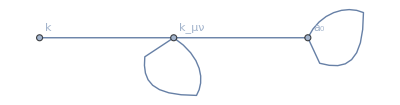

```mathematica
nG=1;nS=0;isGravity=True;

rawBase=Join[{2,0},Table[1,{i,nG}],Table[0,{i,nS}]];
{rawBP,rawBom}=ComputeOp[fluct,isGravity,gaugeFields,gaugeVecs,scalars];//Timing
graph=WhichCouplings[rawBP,rawBom,True,gaugeFields,gaugeVecs,scalars];
Vertices={Subscript[k, μν],k,Subscript[a, 0]};
AdjacencyGraph[graph,DirectedEdges->False,VertexLabels->Table[i-> Vertices[[i]],{i,Length[Vertices]}]]
```

```mathematica
CheckOpFluct[fluct,rawBP,rawBom,True,gaugeFields,gaugeVecs,scalars]
```

Reconstruction of the fluctuation operator.
Remains: -a_1 | 1 |   |   
  | a | ;b a_1 | 1 | a | ;b
  |   |

We now compute  Tr E,Tr E^2, Tr Ω^2.

```mathematica
{BP,Bom,Bbase}={rawBP,rawBom,rawBase};

BE=ComputeE[BP,Bbase,Bom]//Simp;
BTrE=TrE[BE,Bbase]//Simp;
BTrEE=TrSq[BE,Bbase]//Simp;

BOm=ComputeOm[Bom,Bbase];
BOm=BOm//Simp;
BTrOmOm=TrSqO[BOm,Bbase];
```

The Seeley-DeWitt coefficients are then given as

```mathematica
TrOne=If[isGravity,9+1,0]+4 nG+nS;

a0EMraw=TrOne;
a2EMraw=BTrE+TrOne/6 Rs;
a4EMraw=1/2 BTrEE+1/6 Rs BTrE+1/12 BTrOmOm+TrOne/360(5 Rs^2+2RR-2RicRic);
```

The results for the ghosts are

```mathematica
TrghOne=If[isGravity,8,0]+2 nG;
BghTrE=If[isGravity,2RicciScalarCD[],0];
BghTrEE=If[isGravity,2RicRic,0];
BghTrOmOm=If[isGravity,-2RR,0];

a0EMghosts=-TrghOne;
a2EMghosts=-( BghTrE+TrghOne/6 Rs);
a4EMghosts=-(1/2 BghTrEE+1/6 Rs BghTrE+1/12 BghTrOmOm+TrghOne/360(5 Rs^2+2RR-2RicRic));
```

The total Seeley-DeWitt coefficients are then

```mathematica
a0EM=a0EMraw+a0EMghosts
a2EM=a2EMraw+a2EMghosts//TC
a4EM=a4EMraw+a4EMghosts//FC
```

4

6 F |   |  
a | b F | a | b
  |  -(10 R[▽])/3

13/90 R[▽] |   |  
a | b R[▽] | a | b
  |  -(7 R[▽]^2)/9+199/180 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4EM//FDecompose
```

Remains: 0

Value: -(53 Euler)/45+(137 Weyl^2)/60-(13 R[▽]^2)/36

{-53/45,137/60,-13/36,0}

## N=2 gravitini

### Lagrangian

We input the Lagrangian in the matrix L. We set here l_AdS=1, it is reinstated at the end of the computation.

```mathematica
Fbase={1};
nGrav=1;nGaug=0;

FL=0IdentityMatrix[Length[Fbase]];

FL[[1,1]]= ⅈ  gmn[a,b]gamma[c,-α,β]Ac[-c]-ⅈ/2 Raise[multiDot[Fc[a,b] ,tp[gammaU,tp[gammaUU,gammaU]],{{1,1},{2,4}}]]-gammaUU;
FL=FL//gSimp//Simplify;

FP=fComputeP[FL,Fbase]//gSimp;
Fom=fComputeom[FL,Fbase]//gSimp;
```

We compute E, Ω and their traces

```mathematica
FE=fComputeE[FP,Fbase,Fom];//Timing
```

{96.6115,Null}

```mathematica
FE=FE//gSimp//fSimp;
FTrE=fTr[TrE[FE,Fbase]]//gSimp//fSimp;
FTrEE=fTrSq[FE,Fbase];
```

```mathematica
FTrEE=FTrEE//sumSimp;//Timing
```

{68.7481,Null}

```mathematica
FOm=fComputeOm[Fom,Fbase];//Timing
FTrOmOm=fTrSqO[FOm,Fbase];//Timing
```

{107.146,Null}

{0.120638,Null}

```mathematica
FTrOmOm=FTrOmOm//sumSimp;//Timing
```

{111.829,Null}

The Seeley-DeWitt coefficients are

```mathematica
FTrOne=16  nGrav +4 nGaug ;

a0Fgrav=(-1/2)FTrOne;
a2Fgrav=(-1/2)(FTrE+FTrOne/6 Rs)//fSimp;
a4Fgrav=(-1/2)(1/2 FTrEE +1/6 Rs FTrE+1/12 FTrOmOm+FTrOne/360(5 Rs^2+2RR-2RicRic))//fSimp//FourDualCanon;
```

The final result is multiplied by two for the two gravitini

```mathematica
2a4Fgrav//FC//FDecompose
```

Remains: 0

Value: (139 Euler)/90-(32 Weyl^2)/15+8/9 F |   |  
a | b F | a | b
  |   R[▽]-(2 R[▽]^2)/9

{139/90,-32/15,-2/9,8/9}

### Ghosts

We compute the ghost contribution for a general value mG of the mass.

```mathematica
DefConstantSymbol[mG]
```

** DefConstantSymbol: Defining constant symbol mG.

```mathematica
Ghbase={0};
GhL=IdentityMatrix[Length[Ghbase]];

GhL[[1,1]]=(2 mG)/lAdS gamma[LI[6],-α,β]+  ⅈ/lAdS gamma[c,-α,β]Ac[-c]//gSimp;

GhP=fComputeP[GhL,Ghbase];
Ghom=fComputeom[GhL,Ghbase]//gSimp;
```

```mathematica
GhE=fComputeE[GhP,Ghbase,Ghom]//gSimp//fSimp;
GhTrE=fTrE[GhE,Ghbase]//gSimp//fSimp;
GhTrEE=fTrSq[GhE,Ghbase]//gSimp//fSimp;
```

```mathematica
GhOm=fComputeOm[Ghom,Ghbase];
GhTrOmOm=fTrSqO[GhOm,Ghbase]//gSimp//fSimp;//Timing
```

{1.58969,Null}

```mathematica
GhTrOne=4 Length[Ghbase];

a0Fghost=(-1/2)GhTrOne;
a2Fghost=(-1/2)(GhTrE+GhTrOne/6 Rs);
a4Fghost=(-1/2)(1/2 GhTrEE +1/6 Rs GhTrE+1/12(GhTrOmOm)+GhTrOne/360(5 Rs^2+2RR-2RicRic))//FourDualCanon;
```

```mathematica
a4Fghost//FDecompose
```

Remains: 0

Value: -(11 Euler)/720+Weyl^2/40+1/36 F |   |  
a | b F | a | b
  |   R[▽]+1/18 (mG^2-2 mG^4) R[▽]^2

{-11/720,1/40,1/18 (mG^2-2 mG^4),1/36}

### Result

The total Seeley-DeWitt coefficients are

```mathematica
a0F=2(a0Fgrav-(a0Fghost/.mG->0)-2(a0Fghost/.mG->1));
a2F=2(a2Fgrav-(a2Fghost/.mG->0)-2(a2Fghost/.mG->1))//TC;
a4F=2(a4Fgrav-(a4Fghost/.mG->0)-2(a4Fghost/.mG->1))//FC
```

-89/45 R[▽] |   |  
a | b R[▽] | a | b
  |  +13/18 F |   |  
a | b F | a | b
  |   R[▽]+(7 R[▽]^2)/8-233/360 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

```mathematica
a4F//FDecompose
```

Remains: 0

Value: (589 Euler)/360-(137 Weyl^2)/60+13/18 F |   |  
a | b F | a | b
  |   R[▽]

{589/360,-137/60,0,13/18}

#### Minimal gauged supergravity

The bosonic and fermionic contributions computed above are:

```mathematica
a0B=4;
a2B=6 {{F, {{, }, {a, b}}}} {{F, {{a, b}, {, }}}}-(10 R[▽])/3;
a4B=13/90 {{R[▽], {{, }, {a, b}}}} {{R[▽], {{a, b}, {, }}}}-(7 R[▽]^2)/9+199/180 {{R[▽], {{, , , }, {a, b, c, d}}}} {{R[▽], {{a, b, c, d}, {, , , }}}};

a0F=-4;
a2F=-8 {{F, {{, }, {a, b}}}} {{F, {{a, b}, {, }}}}+7 R[▽];
a4F=-89/45 {{R[▽], {{, }, {a, b}}}} {{R[▽], {{a, b}, {, }}}}+13/18 {{F, {{, }, {a, b}}}} {{F, {{a, b}, {, }}}} R[▽]+(7 R[▽]^2)/8-233/360 {{R[▽], {{, , , }, {a, b, c, d}}}} {{R[▽], {{a, b, c, d}, {, , , }}}};
```

```mathematica
a0=a0B+a0F
a2=a2B+a2F//TC
a4=a4B+a4F//FC
```

0

-2 F |   |  
a | b F | a | b
  |  +(11 R[▽])/3

-11/6 R[▽] |   |  
a | b R[▽] | a | b
  |  +13/18 F |   |  
a | b F | a | b
  |   R[▽]+(7 R[▽]^2)/72+11/24 R[▽] |   |   |   |  
a | b | c | d R[▽] | a | b | c | d
  |   |   |

The final result for a_4 is

```mathematica
a4//FDecompose
```

Remains: 0

Value: (11 Euler)/24+13/18 F |   |  
a | b F | a | b
  |   R[▽]-(13 R[▽]^2)/36

{11/24,0,-13/36,13/18}